Figure out the value of a resistor from an image

Delgadillo Itzel

Espigulé Jofre

Universidad Panamericana

Most representative image

-Graphics-

Abstract

GOAL OF THE PROJECT: To output the value of a resistor given a photo of it. The photos are intended to be taken in a white background, like from a white paper sheet and with a cellphone camera.

SUMMARY OF WORK: Many samples are used in a Classifier, leaving as result a logistic regression, all training and test samples were rotated and cropped automatically. The resistor position is found using morphological components, then the picture is cropped and rotated leaving the resistor to cover the majority of the picture, using the Classifier we obtain the final result.

RESULTS AND FUTURE  WORK: The project is limited to a small set of resistors to which it can calculate the value. The next step is to either to crop the color bands of the resistor only, and use machine learning in a similar way to obtain the color of each of the bands of the resistor, or improve the current methods to raise the extent of the project.

Everything above this bar is your poster. Make sure it fits on a single page. "Preview Poster"

Additional concise content for 2 minute presentation

-Graphics-

Everything above this bar is in your 2 minute presentation. "Preview Presentation"

Detailed Records of the Project

Main Results in Detail

The first approach that was made to solve the problem was given by the Lecture Notes in Computer Science [1] document, in it a similar problem is tried to be resolved. The difference was that the resistor photos were taken in an environment where the light is controlled, avoiding the glare.

The first step was to obtain the background color of the image, this was originally done obtaining the mean of the pixels near the edges of the picture, in this case it was done obtaining a mask to identify the background and obtaining the mean of all the pixels in it.

```mathematica
img = -Graphics-;
img = ImageAdjust[ImageResize[img, {500}]];
img = ColorConvert[RemoveAlphaChannel[img],"RGB"];
```

```mathematica
meanColorMask[image_,mask_ ]:= Module[
{toRemove,imgList},
toRemove = PixelValuePositions[mask, Black];
imgList = Transpose @ ImageData[image];
imgList = Delete[imgList, toRemove];
RGBColor[Mean[Catenate @ imgList]]
]
```

```mathematica
getBackColor[image_] := meanColorMask[image, ColorNegate @ AlphaChannel[RemoveBackground[image]]];
backColor = getBackColor[img]
```

RGBColor[{0.4647289741747594, 0.46767765548741147, 0.4936690884215208}]

This color is subtracted from the image, then the result of that is converted to grayscale.

```mathematica
absoluteSubstract[image_, color_] := ImageApply[
	MapThread[
		Abs[#1 - #2]&,
		{Flatten[#],Flatten[List @@ color]}
	]&,
	image
]
substracted = absoluteSubstract[img, backColor]
monochromatic = ColorConvert[substracted,"Grayscale"]
```

-Graphics-

-Graphics-

From here we calculate a threshold we are going to use to separate the resistor from the background. This method is further explained in [1] and [2]

```mathematica
threshold[n_] := Module[
	{num, p, ω, μ, μT, maxK, maxσ, σ2B, temp, k},
	num = Total[n];
	p = n / num;
	ω := Sum[p[i],{i,0,#}]&;
	μ := Sum[(i+1) * p[i], {i, 0, #}]&;
	μT = μ[255];
	σ2B[x_Integer] := Module[
		{μk, ωk},
		ωk = ω[x];
		μk = μ[x];
		If[ ωk ≠ 0 && ωk ≠ 1,
			((μT*ωk - μk)^2) / (ωk * (1 - ωk)),
			-1
		]
	];
	maxσ = 0;
	maxK = 255;
	For[k = 0, k < 255, k++,
		temp = σ2B[k];
		If[ NumberQ[temp] && temp > maxσ,
			maxσ = temp;
			maxK = k;
		]
	];
	maxK
]
```

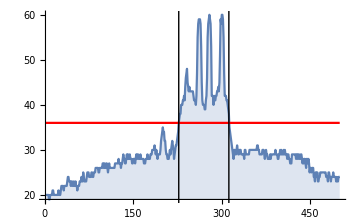
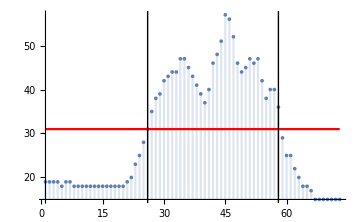
-Graphics- | -Graphics-
Horizontal mean | Vertical mean

-Graphics-

```mathematica
matr = ImageData[monochromatic];
verMean = Map[
	Mean[Flatten[#]]&,
	matr
];
verMean = Round[verMean * 255];
horMean = Map[
	Mean[Flatten[#]]&,
	Transpose[matr]
];
horMean = Round[horMean * 255];

horFrequency = Counts[Catenate[{horMean,Range[0,255]}]] - 1;
verFrequency = Counts[Catenate[{verMean,Range[0,255]}]] - 1;
verThreshold = threshold[verFrequency];
horThreshold = threshold[horFrequency];

verPlot = DiscretePlot[
	verMean[[x]],
	{x, 1, Length[verMean]},
	PlotRange->All,
	ImageSize->Medium
];
verThresholdPlot = Plot[
	verThreshold,
	{x, 1, Length[verMean]},
	PlotRange->All,
	ImageSize->Medium,
	PlotStyle->{Red}
];

horPlot = DiscretePlot[
	horMean[[x]],
	{x, 1, Length[horMean]},
	PlotRange->All,
	ImageSize->Medium
];
horThresholdPlot = Plot[
	horThreshold,
	{x, 1, Length[horMean]},
	PlotRange->All,
	ImageSize->Medium,
	PlotStyle->{Red}
];

xPos = Values @ Cases[
	MapIndexed[#1->First[#2]&, horMean],
	(x_->y_)/;x>= horThreshold
];
xStart = Min[xPos];
xEnd = Max[xPos];

yPos = Values @ Cases[
	MapIndexed[#1->First[#2]&, verMean],
	(x_->y_)/;x>= verThreshold
];
yStart = Min[yPos];
yEnd = Max[yPos];

segmented = ImageTake[
	img,
	{yStart, yEnd},{xStart, xEnd}
];
xStartLine = Graphics @ Line[{{xStart, 0},{xStart, 255}}];
xEndLine = Graphics @ Line[{{xEnd, 0},{xEnd, 255}}];
yStartLine = Graphics @ Line[{{yStart, 0},{yStart, 255}}];
yEndLine = Graphics @ Line[{{yEnd, 0},{yEnd, 255}}];
Grid[{
	{
		Show[{horPlot, horThresholdPlot, xStartLine, xEndLine}],
		Show[{verPlot, verThresholdPlot, yStartLine, yEndLine}]
	},
	{"Horizontal mean", "Vertical mean"}
}]
segmented
```

The graphs represent the average color of each of the columns and rows of the pixels of the monochromatic image. The threshold for each of them is represented with the red line and is calculated using the Otsu’s method. The black lines represent the left-most, right-most columns, and top and bottom rows where the mean color is over the threshold. With those values we can cut the resistor of the image.
Finally, in this approach we extract an image with a height of 15 pixels.

```mathematica
extracted = ImageCrop[segmented, {ImageDimensions[segmented][[1]], 15}, Center]
```

-Graphics-

A similar method is used for obtaining the bands, however, the K-means method did not result convenient for our use case, as kept marking the glare in the resistor as part of the band.

```mathematica
extracted = ImageResize[extracted, {500}];
exBackColor = 
ColorConvert[
	Hue @@ ImageMeasurements[ColorConvert[extracted, "HSB"], "Mean"],
	"RGB"
]
exSubs = 
TotalVariationFilter @ absoluteSubstract[
	extracted,
	ColorConvert[exBackColor,"RGB"]
]
exMono = ColorConvert[exSubs, "Grayscale"]
exBinary = Binarize[exMono,Method->"Cluster"]
allX = Map[
	Interval[{Ramp[Min[#]],Ramp[Max[#]]}]&,
	Values[ComponentMeasurements[
		MorphologicalComponents[exBinary],
		"MinimalBoundingBox"
	]][[All, All, 1]]
];
allX = List @@ (IntervalUnion @@ allX);
squaresX = Polygon @ Map[
	Module[
		{min, max, height},
		min = #[[1]];
		max = #[[2]];
		height = ImageDimensions[extracted][[2]];
		{{min, 1}, {min, height}, {max, height}, {max, 1}}
	]&,
	allX
];
HighlightImage[extracted, {Red, squaresX}]
```

RGBColor[0.23696657040633345, 0.2562154608969708, 0.17074789625041814]

-Graphics-

-Graphics-

-Graphics-

-Graphics-

The next approach was to use machine learning to obtain the values of the resistors. Several samples were made taking pictures from resistors on a white background, making sure they had different positions and angles. However, the training was taking too long and causing the Mathematica program to crash. Later it was concluded that the results would improve if the resistor in the photo was cropped, removing several pixels without any information the total memory needed to process the images would be lower.

For cropping the resistor from the photo, the next was made:

Pass the photo through ImageAdjust and BrightnessEqualize rise the contrast and remove shadows from the image.

Used the function RemoveBackground to obtain from the alpha channel a mask that would separate the resistor from the background.

Erode said mask, so the wires in the resistor are eliminated from the mask.

Use RegionBinarize to recover the parts of the resistor that were removed from the mask.

Obtain the minimal bounding box and orientation angle from this resistor mask.

Rotate and crop the image according with the previous values.

```mathematica
resistorCrop[image_] := Module[
	{preprocess, angle, rotated, newPoints, allX, allY, minX, minY, maxX, maxY, processed, adjusted},
	adjusted = ImageAdjust @ BrightnessEqualize[image];
	preprocess = SelectComponents[Erosion[AlphaChannel[RemoveBackground[adjusted]],10],"Count",-1];
	preprocess = RegionBinarize[adjusted,preprocess,0.15];
	processed = MorphologicalComponents[preprocess];
	angle = First @ Values[
		ComponentMeasurements[processed, "Orientation"]
	];
	rotated = ImageRotate[image, -angle, Masking->Full];
	newPoints = First @ Values[ComponentMeasurements[processed, "MinimalBoundingBox"]];
	newPoints = RotationTransform[-angle,ImageDimensions[image]/2][newPoints];
	newPoints = TranslationTransform[(ImageDimensions[rotated] - ImageDimensions[image])/2][newPoints];
	allX = newPoints[[All, 1]];
	allY = newPoints[[All, 2]];
	minX = Min[allX];
	minY = Min[allY];
	maxX = Max[allX];
	maxY = Max[allY];
	ImageTake[rotated, Ramp[ImageDimensions[rotated][[2]]-{maxY, minY}],{minX,maxX}]
]
```

From this function the samples would be cropped to allow the training to run faster. Some images were not cropped correctly and had to be removed.

This method can not be used for the final product though, as it runs really slow. One way to make a faster method is to rescale the initial image smaller before obtaining the mask and at the end rescale the cropping coordinates accordingly, reducing the total pixels the program would work on. Naturally this method is less precise.

```mathematica
resistorLightCrop[image_] := Module[
	{preprocess, angle, rotated, newPoints, allX, allY, minX, minY, maxX, maxY, processed, adjusted, resized, prop, fullRotated},
	resized = ImageResize[image, {500}];
	prop = ImageDimensions[image][[1]] / ImageDimensions[resized][[1]];
	adjusted = ImageAdjust @ BrightnessEqualize[resized];
	preprocess = SelectComponents[Erosion[AlphaChannel[RemoveBackground[adjusted]],10 / prop],"Count",-1];
	preprocess = RegionBinarize[adjusted,preprocess,0.15];
	processed = MorphologicalComponents[preprocess];
	angle = First @ Values[
		ComponentMeasurements[processed, "Orientation"]
	];
	rotated = ImageRotate[resized, -angle, Masking->Full];
	newPoints = First @ Values[ComponentMeasurements[processed, "MinimalBoundingBox"]];
	newPoints = RotationTransform[-angle,ImageDimensions[resized]/2][newPoints];
	newPoints = TranslationTransform[(ImageDimensions[rotated] - ImageDimensions[resized])/2][newPoints];
	allX = newPoints[[All, 1]];
	allY = newPoints[[All, 2]];
	minX = Min[allX];
	minY = Min[allY];
	maxX = Max[allX];
	maxY = Max[allY];
	fullRotated = ImageRotate[image, -angle, Masking->Full];
	ImageTake[fullRotated, Ramp[ImageDimensions[fullRotated][[2]]-{maxY * prop, minY * prop}],{minX * prop,maxX * prop}]
]
SetDirectory[NotebookDirectory[]];
DumpSave["resistorLightCrop.mx", resistorLightCrop];
ResetDirectory[];
```

Once the images of the dataset are loaded we need to create the training set and the test set.

As the cropping method used in the training is more accurate than the one used for the final product, we are going to need to add noise to the samples to improve the results. This is because the method used has shown to fail sometimes in rotating the resistor, especially if the wires in the resistor are bended, so we then add more samples were the resistor is rotated to random angles to make the Classifier be prepared if the cropping function fails to make the rotation. We also add blurry samples using a GaussianFilter. As for the Classifier method, a simple Classify function with a quality performance goal is used.

```mathematica
newBlurry[data_, n_] :=
Module[
	{toBlur},
	toBlur = RandomSample[data, n];
	toBlur/.(x_->y_):>GaussianFilter[x,15]->y
]
```

```mathematica
newRotated[data_, n_] := 
Module[
	{toRotate},
	toRotate = RandomSample[data, n];
	toRotate/.(x_->y_):>ImageRotate[x,RandomReal[{0, π}], Masking->Full]->y
]
```

```mathematica
newBlurry[trainingSet, 1]
```

{-Graphics-→2200}

```mathematica
newRotated[trainingSet, 1]
```

{-Graphics-→220000}

This improved not only the accuracy for the given samples, but also the results on the final product.

```mathematica
cNoParametersM = ClassifierMeasurements[cNoParameters, testSet]
```

ClassifierMeasurementsObject[…]

```mathematica
cNoParametersM["ConfusionMatrixPlot"]
```

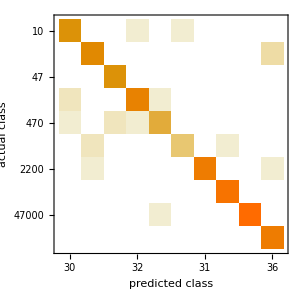

Code

https://github.com/carolinadp/WSS2017

Written Content / Lesson Plans

Conclusions in Detail

The machine learning method used at the moment is limited to the resistor values it is trained with. It is done this way to provide a proof of concept to show that machine learning methods can be used to distinguish between resistor colors, as it has shown it is able to do so between the whole resistors.
Cropping the bands has not been effective at the moment because of the glare on the resistors. As the resistors usually have very reflective surfaces this made the band detection very difficult.

-Graphics-

-Graphics-

-Graphics-

-Graphics-

As shown at the pictures, the glare would modify the components in the image, making the program believe there are more color bands or that they are wider.

All Visualizations

```mathematica
-Graphics-
-Graphics-
```

Data Sources Links/References

Future Directions

The next direction for this project is going to be to look for a way to generalize this project. This might mean to find a effective way to extract the color bands from a given photo of a resistor. Given that it was possible to make machine learning to recognize complete resistor, it should be possible to do this with single color bands.

Other option for generalize the project could be to design a better way to make a machine learning method instead of just using the classifier, so there can be a way for it to calculate the value of the resistance. Given that the color bands in the resistors represent either a digit or an exponent it might be possible to teach that pattern.

Background Info Links/References

[1] Mitani Y., Sugimura Y., Hamamoto Y. (2008) A Method for Reading a Resistor by Image Processing Techniques. In: Lovrek I., Howlett R.J., Jain L.C. (eds) Knowledge-Based Intelligent Information and Engineering Systems. KES 2008. Lecture Notes in Computer Science, vol 5177. Springer, Berlin, Heidelberg

[2] Otsu N. A Threshold Selection Method from Gray-Level Histograms. IEEE Transactions on Systems, Man and Cybernetics. 1979

Keywords

Provide keywords as items

Image processing

Machine learning

Resistor

Other

Date

Last Modified: Wednesday, July 05, 2017

```mathematica
"Add Timestamp"
```